```mathematica
referenceChebyshev[n_]:=Sum[MangoldtLambda[j],{j,2,n}]
num[c_]:=Numerator[c];den[c_]:=Denominator[c]
alpha[n_,c_]:=alpha[n,c]=den[c] (Floor[n/den[c]]-Floor[(n-1)/den[c]])-num[c] (Floor[n/num[c]]-Floor[(n-1)/num[c]])
F[n_,0,s_,c_]:=1
F[n_,1,s_,c_]:=If[n<s,0,(den[c] Floor[n/den[c]]-num[c] Floor[n/num[c]])-(den[c] Floor[(s-1)/den[c]]-num[c] Floor[(s-1)/num[c]])]
F[n_,k_,s_,c_]:=F[n,k,s,c]=Sum[If[alpha[m,c]==0,0,Binomial[k,j] alpha[m,c]^j F[Floor[n/(m^j)],k-j,m+1,c]],{j,1,k},{m,s,Floor[n^(1/k)]}]
E1Alt[n_,k_,c_]:=den[c]^-k F[n den[c]^k,k,1,c]
E2Alt[n_,k_,c_]:=den[c]^-k F[n den[c]^k,k,den[c]+1,c]
E2[n_,k_,c_]:=E2[n,k,c]=(1/den[c])Sum[If[alpha[j,c]==0,0,alpha[j,c]E2[(den[c] n)/j,k-1,c]],{j,den[c]+1,den[c] n}];E2[n_,0,c_]:=1
E1[n_,z_,c_]:=Sum[Binomial[z,k] E2[n,k,c],{k,0,Floor[Log[If[ c<2,c,2],n]]}]
e1[n_, z_, c_] := E1[n,z,c] - E1[n-1,z,c]
L2[n_,k_,c_]:=L2[n,k,c]=(1/den[c])Sum[If[alpha[j,c]==0,0,alpha[j,c] Log[j/den[c]]E2Alt[den[c] n/j,k-1,c]],{j,den[c]+1,den[c] n}];L2[n_,0,c_]:=1
ChebAlt[n_,c_]:=1+Sum[(-1)^(k-1) L2[n,k,c],{k,0,Floor[Log[n]/Log[If[c<2,c,2]]]}]+Sum[c^k Log[c],{k,1,Floor[Log[n]/Log[c]]}]
bin[z_,k_]:=Product[z-j,{j,0,k-1}]/k!
L1[n_,z_,c_]:=L1[n,z,c]=Sum[bin[z,k] L2[n,k,c],{k,1,Floor[Log[If[ c < 2, c, 2],n]]}]
l1[n_, z_, c_] := FullSimplify[L1[n,z,c]-L1[n-1,z,c]]
L2a[n_,1,c_]:=L2a[n,1,c]=(1/den[c])Sum[alpha[j,c]Log[j/den[c]],{j,den[c]+1,den[c] n}]
L2x[n_,1,b_]:=L2x[n,1,b]=Sum[Log[j],{j,2,n}]-b Sum[Log[j b],{j,1,n/b}]
L2x[n_,k_,b_]:=Sum[L2x[n/j,k-1,b],{j,2,n}]-b Sum[L2x[n/(j b),k-1,b],{j,1,n}]
E2x[n_,k_,x_]:=E2x[n,k,x]=Sum[E2x[n/j,k-1,x],{j,2,n}]-x Sum[E2x[n/(x j),k-1,x],{j,1,n/x}];E2x[n_,0,x_]:=1
E1x[n_,z_,c_]:=Sum[Binomial[z,k] E2x[n,k,c],{k,0,Floor[Log[If[ c<2,c,2],n]]}]
e1x[n_, z_, c_] := E1x[n,z,c] - E1x[n-1,z,c]
L1x[n_,z_,x_]:=L1x[n,z,x]=Sum[bin[z,k] L2x[n,k,x],{k,1,Floor[Log[If[ x < 2, x, 2],n]]}]
l1x[n_, z_, x_] := l1x[n,z,x] = L1x[n,z,x]-L1x[n-1,z,x]
L1y[ n_, 0, c_] := 0
L1y[n_, k_, c_] := den[c]^-1 Sum[ alpha[j,c]( Log[j/den[c]]+ L1y[ n den[c] / j, k-1, c]), {j, 1, den[c] n}]
l1y[n_, k_, c_] := den[c]^-1 Sum[ alpha[j,c]( Log[j/den[c]]+ L1y[ n den[c] / j, k-1, c]), {j, 1, den[c] n}]-den[c]^-1 Sum[ alpha[j,c]( Log[j/den[c]]+ L1y[ (n den[c]-1) / j, k-1, c]), {j, 1, den[c] n-1}]
L1w[n_,0,b_]:=0
L1w[n_,k_,b_]:=Sum[Log[j] + L1w[n/j,k-1,b],{j,1,n}]-b Sum[ Log[ j b ] + L1w[n/(j b),k-1,b],{j,1,n}]
```

```mathematica
num[c_]:=Numerator[c];den[c_]:=Denominator[c]
alpha[n_,c_]:=den[c] (Floor[n/den[c]]-Floor[(n-1)/den[c]])-num[c] (Floor[n/num[c]]-Floor[(n-1)/num[c]])
ChebAlt2[n_,c_]:=Sum[(-1)^(k) L2[n,k,c],{k,0,Floor[Log[n]/Log[If[c<2,c,2]]]}]
Lm1[ n_, c_ ] := (1/den[c])Sum[If[alpha[j,c]==0,0,alpha[j,c]( Log[j/den[c]]-Lm1[den[c] n/j,c])],{j,den[c]+1,den[c] n}]
```

```mathematica
1-N[Lm1[ 100, 3/2]]
```

```mathematica
10.953519285239476
```

```mathematica
N[ChebAlt2[100,3/2]]
```

10.9535

```mathematica
Sum[ N[Lm1[100/j,2]], {j,1,100}]
```

```mathematica
d-18.877868113526315
```

```mathematica
Sum[ N[ (-1)^(j+1) Log[j]],{j,1,100}]
```

-2.53088

```mathematica
{Sum[ e1[ j, -1, 2 ]N[L1[Floor[100/j],1,2]],{j,1,100}], -N[L1[ 100, -1, 2]]}
```

{6.70877,6.70877}

```mathematica
{Sum[ e1[ j, 1, 2 ]N[L1[Floor[100/j],-1,2]],{j,1,100}], -N[L1[ 100, 1, 2]]}
```

{2.53088,2.53088}

```mathematica
{Sum[ E1[ 100/j, -1, 2 ]N[alpha[ j, 2]Log[j]],{j,1,100}], -N[L1[ 100, -1, 2]]}
```

{6.70877,6.70877}

```mathematica
{Sum[ e1x[ j, -1, 2 ]N[L1x[Floor[100/j],1,2]],{j,1,100}], -N[L1[ 100, -1, 2]]}
```

{6.70877,6.70877}

```mathematica
{Sum[ E1x[ 100/j, -1, 2 ]N[l1x[j,1,2]],{j,1,100}], -N[L1[ 100, -1, 2]]}
```

{6.70877,6.70877}

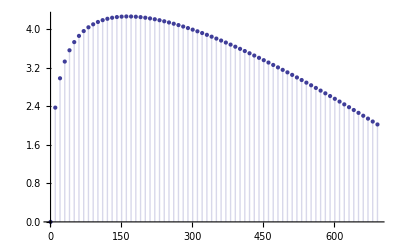

```mathematica
L2b[n_,1,c_]:=(1/den[c])Sum[alpha[j,c]Log[j/den[c]],{j,den[c]+1,den[c] n}]
DiscretePlot[ L2a[ n, 1,1001/1000], {n,1,700, 10}]
```

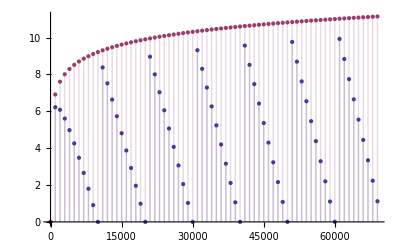

```mathematica
DiscretePlot[ { L2x[ n, 1,10001/10000], Log[n]}, {n,1,70000, 1000}]
```

```mathematica
{(1/2)Sum[ E1[ (2 10)/j, -1, 3/2 ]N[alpha[ j, 3/2]Log[j/2]],{j,1,2 10}], -N[L1[ 10, -1, 3/2]]}
```

{-0.188592,-0.188592}

```mathematica
{(1/3)Sum[ E1[ (3 100)/j, -1, 4/3 ]N[alpha[ j, 4/3]Log[j/3]],{j,1,3 100}], -N[L1[ 100, -1, 4/3]]}
```

{-19.6174,-19.6174}

```mathematica
ld[ n_, c_] := den[c]^-1 Sum[ E1[ n den[c]/j, -1, c ]N[alpha[ j, c]Log[j/den[c]]],{j,1,n den[c]}]
ldx[ n_, c_] := den[c]^-1 Sum[ E1x[ n den[c]/j, -1, c ]N[alpha[ j, c]Log[j/den[c]]],{j,1,n den[c]}]
```

```mathematica
{ ldx[ 200, 11/10], -N[L1[ 200, -1, 11/10]]}
```

{8.9824,8.9824}

```mathematica
{(1/2)Sum[ E1[ (2 100)/j, -1, 3/2 ]N[alpha[ j, 3/2]Log[j/2]],{j,1,2 100}], -N[L1[ 100, -1, 3/2]]}
```

```mathematica
L2y[n_,1,b_]:=Sum[Log[j],{j,2,n}]-b Sum[Log[j b],{j,1,n/b}]
{(1/2)Sum[ e1[ j, -1, 3/2 ]N[L2y[Floor[2 10/j],1,3/2]],{j,1,2 10}], -N[L1[ 10, -1, 3/2]]}
```

{-2.27449,-0.188592}

```mathematica
{(1/2)Sum[ e1[ j, -1, 3/2 ]N[Sum[ alpha[ m, 3/2]Log[m/2],{m,1,Floor[2 100/j]}]],{j,1,2 100}], -N[L1[ 100, -1, 3/2]]}
```

{-16.1766,-9.95352}

```mathematica
Table[ alpha[j,3/2],{j,1,20}]
```

{0,2,-3,2,0,-1,0,2,-3,2,0,-1,0,2,-3,2,0,-1,0,2}

```mathematica
N[(1/2)Sum[Sum[  e1[j, -1, 3/2],{j,1,Floor[10 2/k]}]  alpha[k,3/2] Log[ k/2],{k,1,2 10}]]
```

-1.96394

```mathematica
N[(1/2)Sum[E1[10 2/k, -1, 3/2]  alpha[k,3/2] Log[ k/2],{k,1,2 10}]]
```

-0.188592

```mathematica
N[(1/2)Sum[E1[Floor[10 2/k], -1, 3/2]  alpha[k,3/2] Log[ k/2],{k,1,2 10}]]
```

-1.96394

```mathematica
N[(1/2)Sum[ e1[ j, -1, 3/2] Sum[ alpha[k,3/2] Log[ k/2],{k,1,2 10/j}],{j,1,2 10}]]
```

-1.96394

```mathematica
{(1/2)Sum[ E1[ (2 10)/j, -1, 3/2 ]N[alpha[ j, 3/2]Log[j/2]],{j,1,2 10}], -N[L1[ 10, -1, 3/2]]}
```

{-0.188592,-0.188592}

```mathematica
E1[20,-1,3/2]
```

597/128

```mathematica
Sum[ e1[ j, -1, 3/2],{j,1,20}]
```

597/128

```mathematica
{Sum[ E1[ 100/j, 1, 2 ]N[l1[j,-1,2]],{j,1,100}], -N[L1[ 100, 1, 2]]}
```

{2.53088,2.53088}

```mathematica
{Sum[ E1[ 100/j, -1, 2 ]N[l1[j,1,2]],{j,1,100}], -N[L1[ 100, -1, 2]]}
```

{6.70877,6.70877}

```mathematica
{Sum[ L1[ 100/j, 1, 2 ]N[e1[j,-1,2]],{j,1,100}], -N[L1[ 100, -1, 2]]}
```

{6.70877,6.70877}

```mathematica
{Sum[ L1[ 100/j, -1, 2 ]N[e1[j,1,2]],{j,1,100}], -N[L1[ 100, 1, 2]]}
```

{2.53088,2.53088}

```mathematica
ld[ n_, c_] := den[c]^-1 Sum[ E1[ n den[c]/j, -1, c ]N[alpha[ j, c]Log[j/den[c]]],{j,1,n den[c]}]
```

```mathematica
{(1/2)Sum[ E1[ 2 10/j, 1, 3/2 ]N[l1[j,-1,3/2]],{j,1,2 10}], -N[L1[ 10, 1, 3/2]]}
```

{-0.528475,-1.58635}

```mathematica
{(1/2)Sum[ E1[ 2 10/j, -1, 3/2 ]N[l1[j,1,3/2]],{j,1,2 10}], -N[L1[ 10, -1, 3/2]]}
```

{-1.00113,-0.188592}

```mathematica
ld[10,3/2]
```

-0.188592

```mathematica
{(1/2)Sum[ E1[ 2 10/j, 1, 3/2 ]N[l1y[10, -1,3/2]],{j,1,2 10}], -N[L1[ 10, 1, 3/2]]}
```

```mathematica
FullSimplify[L1[20,1,3/2] - L1[ 19,1,3/2]]
```

-3/2 Log[39/2]+Log[20]

Log[20/3]

```mathematica
N[L1y[ 100, 2, 3/2]]
```

7.75993

```mathematica
N[L1[100,2,3/2]]
```

7.75993

```mathematica
l1dif[n_,1, c_] := den[c]^-1 alpha[den[c]n,c]Log[n]
{FullSimplify[l1dif[ 20, 1,3/2]],alpha[20,3/2]Log[ 20/2]}
```

{Log[20],2 Log[10]}

```mathematica
FullSimplify[l1y[ 20,1,3/2]]
```

Log[20]

```mathematica
lm1[ j_, c_] := N[alpha[ j, c]Log[j/den[c]]]-Sum[ If[ k == 1 || k == j, 0, lm1[k,c]], {k,Divisors[j]}]
```

```mathematica
lm1[ 10, 3/2]
```

3.21888